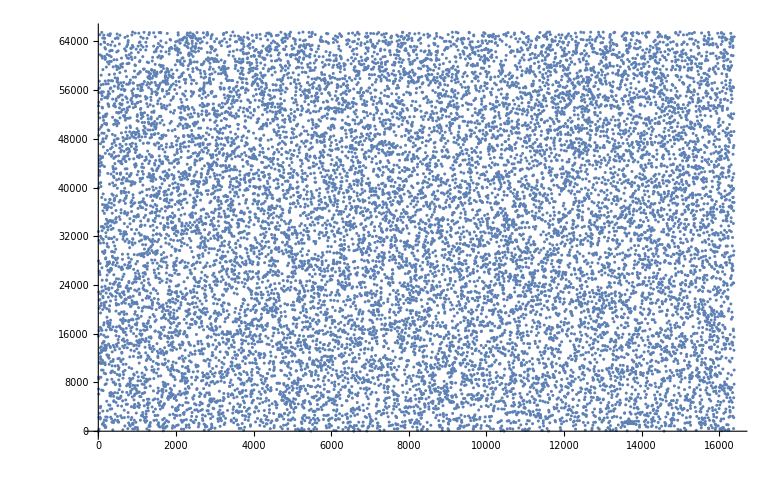
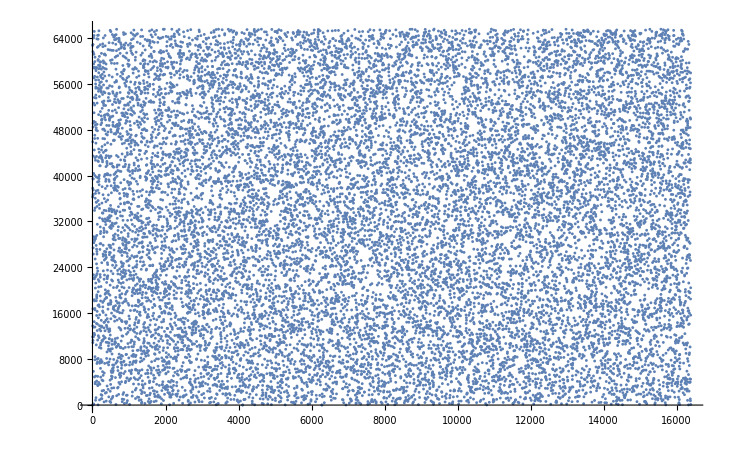
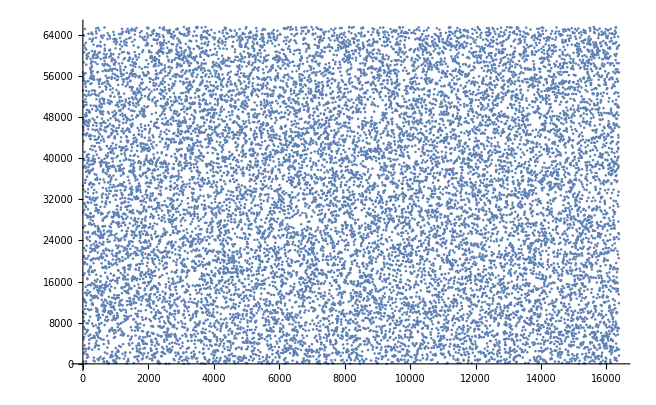
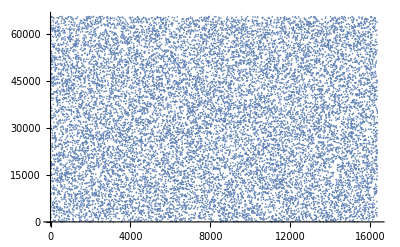
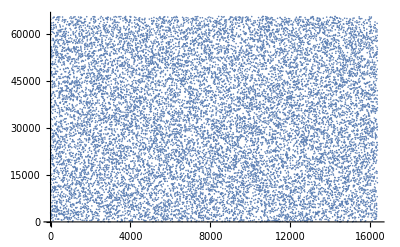
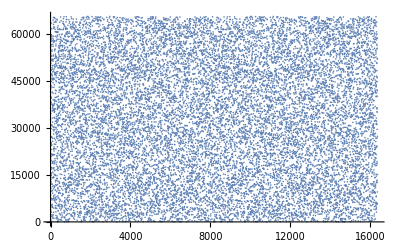
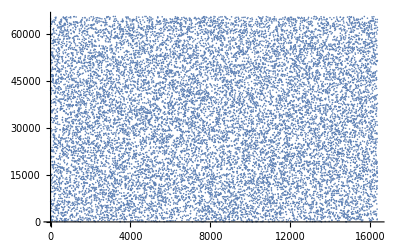
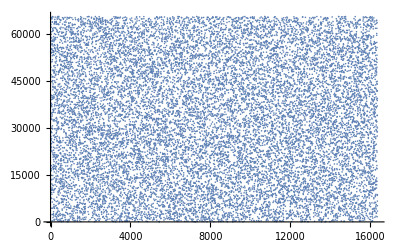
{{{-Graphics-,10,10},{-Graphics-,10,13},{-Graphics-,10,16},{-Graphics-,10,19}},{{-Graphics-,13,10},{-Graphics-,13,13},{-Graphics-,13,16},{-Graphics-,13,19}},{{-Graphics-,16,10},{-Graphics-,16,13},{-Graphics-,16,16},{-Graphics-,16,19}},{{-Graphics-,19,10},{-Graphics-,19,13},{-Graphics-,19,16},{-Graphics-,19,19}}}

```mathematica
nMax=2^14;
mod = NextPrime[2^16];
inv[x_,m_, a_,c_]:=If[
x==0,c,
Mod[
(a*ModularInverse[x,m]+c),
m
]
];

invlk[x_,a_,c_,m_]:=RecurrenceTable[
{
X[n+1]==inv[X[n],m, a,c],
X[1]==x},X,
{n,1,nMax}
];

t = Table[
{
ListPlot[
invlk[1,a,c,mod]
],
a,c
},
{a,10,20,3},{c,10,20,3}]
```